#### General eq $

```mathematica
ClearAll["Global`*"]
λ=1.5418;(*Kα1&Kα2*)
calc[h_,k_,l_,α_,β_,γ_,a_,b_,c_]:=Module[{},
(*unit cell volume*)
V=a b c √(1-Cos[° α]^2-Cos[° β]^2-Cos[° γ]^2+2*Cos[° α]*Cos[° β]*Cos[° γ]);

(*general d-spacing formula*)
d=(V/(√(h^2 b^2 c^2+k^2 a^2 c^2 Sin[° γ]^2+l^2 a^2 b^2-2h k a b^2 c Cos[° γ]^2)));
θ=ArcSin[λ/(2d)]*180/π;
]
"""cellulose Iβ
[1,1,0,90,90,96.5,7.784,8.201,10.380]"""
```

^2 cellulose Iβ
[1,1,0,90,90,96.5,7.784,8.201,10.380]

```mathematica
calc[2,0,0,90,90,96.5,7.784,8.201,10.380];
Print["d(200)= ",d]
Print["2θ(200)= ",Round[2θ,0.1]]

calc[1,1,0,90,90,96.5,7.784,8.201,10.380];
Print["d(110)= ",d]
Print["2θ(110)= ",Round[2θ,0.1]]

calc[1,-1,0,90,90,96.5,7.784,8.201,10.380];
Print["d(1-10)= ",d]
Print["2θ(1-10)= ",Round[2θ,0.1]]
```

d(200)= 3.86698

2θ(200)= 23.

d(110)= 5.65544

2θ(110)= 15.7

d(1-10)= 5.5982

2θ(1-10)= 15.8

```mathematica
(*lattice 'a' dependence*)
temp=7.784;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-1,1,0.1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t200,2θ];
]
tta=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

```mathematica
(*lattice 'b' dependence*)
temp=8.201;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-1,1,0.1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t200,2θ];
]
ttb=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

```mathematica
(*lattice 'γ' dependence*)
temp=96.5;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-10,10,1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t200,2θ];
]
ttg=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

#### Plots

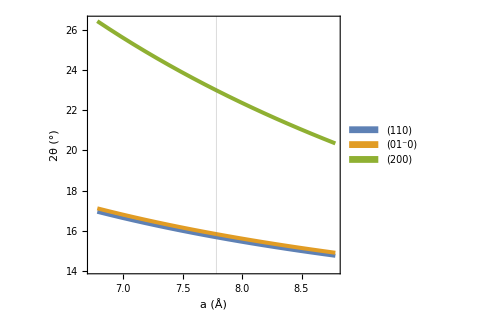

```mathematica
p1=ListLinePlot[{
Table[{tta[[i,1]],tta[[i,2]]},{i,1,Length[n]}],
Table[{tta[[i,1]],tta[[i,3]]},{i,1,Length[n]}],
Table[{tta[[i,1]],tta[[i,4]]},{i,1,Length[n]}]},
GridLines->{{7.784}, None},Frame->True,
FrameLabel->{
Style["a (Å)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.5}],
ImageSize->Medium,AspectRatio->0.9
]
```

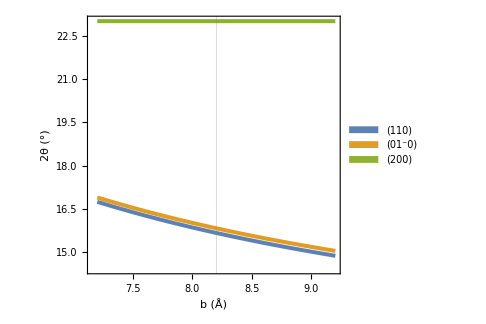

```mathematica
p2=ListLinePlot[{
Table[{ttb[[i,1]],ttb[[i,2]]},{i,1,Length[n]}],
Table[{ttb[[i,1]],ttb[[i,3]]},{i,1,Length[n]}],
Table[{ttb[[i,1]],ttb[[i,4]]},{i,1,Length[n]}]},
GridLines->{{8.201}, None},Frame->True,
FrameLabel->{
Style["b (Å)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.5}],
ImageSize->Medium,AspectRatio->0.9
]
```

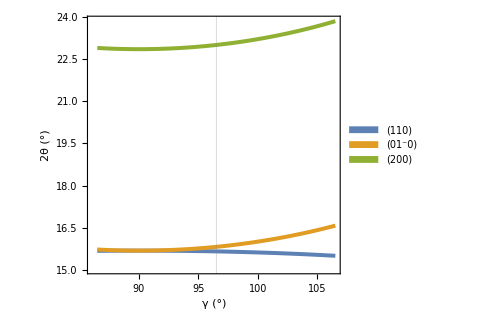

```mathematica
p3=ListLinePlot[{
Table[{ttg[[i,1]],ttg[[i,2]]},{i,1,Length[n]}],
Table[{ttg[[i,1]],ttg[[i,3]]},{i,1,Length[n]}],
Table[{ttg[[i,1]],ttg[[i,4]]},{i,1,Length[n]}]},
GridLines->{{96.5}, None},Frame->True,
FrameLabel->{
Style["γ (°)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.5}],
ImageSize->Medium,AspectRatio->0.9
]
```

#### plot

```mathematica
{p1,p2,p3}
```

{-Graphics-,-Graphics-,-Graphics-}

#### Monoclinic

```mathematica
ClearAll["Global`*"]
λ=1.5418;(*Kα1&Kα2*)
calc[h_,k_,l_,α_,β_,γ_,a_,b_,c_]:=Module[{},
d=(a b c)/(√(a^2 c^2 k^2-2 a b^2 c h l Cot[° β] Csc[° β]+b^2 c^2 h^2 Csc[° β]^2+a^2 b^2 l^2 Csc[° β]^2));
θ=ArcSin[λ/(2d)]*180/π;
];
```

```mathematica
calc[2,0,0,90,90,96.5,7.784,8.201,10.380];
Print["d(200)= ",d]
Print["2θ(200)= ",Round[2θ,0.1]]

calc[1,1,0,90,90,96.5,7.784,8.201,10.380];
Print["d(110)= ",d]
Print["2θ(110)= ",Round[2θ,0.1]]

calc[1,-1,0,90,90,96.5,7.784,8.201,10.380];
Print["d(1-10)= ",d]
Print["2θ(1-10)= ",Round[2θ,0.1]]
```

d(200)= 3.892

2θ(200)= 22.8

d(110)= 5.64578

2θ(110)= 15.7

d(1-10)= 5.64578

2θ(1-10)= 15.7

```mathematica
(*lattice 'a' dependence*)
temp=7.784;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-1,1,0.1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,96.5,n[[j]],8.201,10.380];
AppendTo[t200,2θ];
]
tta2=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

```mathematica
(*lattice 'b' dependence*)
temp=8.201;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-1,1,0.1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,96.5,7.784,n[[j]],10.380];
AppendTo[t200,2θ];
]
ttb2=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

```mathematica
(*lattice 'γ' dependence*)
temp=96.5;
t110={};(*110*)
t110b={};(*1-10*)
t200={};(*200*)
n=Table[temp+i,{i,-10,10,1}];
For[j=1,j<=Length[n],j++,
{h,k,l}={1,1,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t110,2θ];
{h,k,l}={1,-1,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t110b,2θ];
{h,k,l}={2,0,0};
calc[h,k,l,90,90,n[[j]],7.784,8.201,10.380];
AppendTo[t200,2θ];
]
ttg2=Table[{n[[j]],t110[[j]],t110b[[j]],t200[[j]]},{j,1,Length[n]}];
```

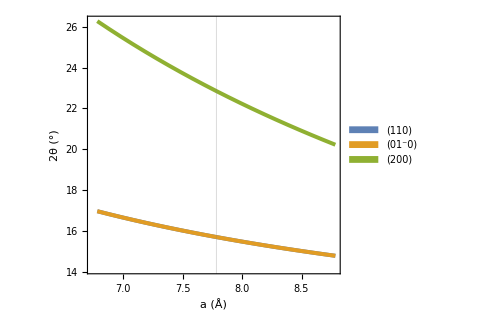

```mathematica
p1=ListLinePlot[{
Table[{tta2[[i,1]],tta2[[i,2]]},{i,1,Length[n]}],
Table[{tta2[[i,1]],tta2[[i,3]]},{i,1,Length[n]}],
Table[{tta2[[i,1]],tta2[[i,4]]},{i,1,Length[n]}]},
GridLines->{{7.784}, None},Frame->True,
FrameLabel->{
Style["a (Å)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.5}],
ImageSize->Medium,AspectRatio->0.9
]
```

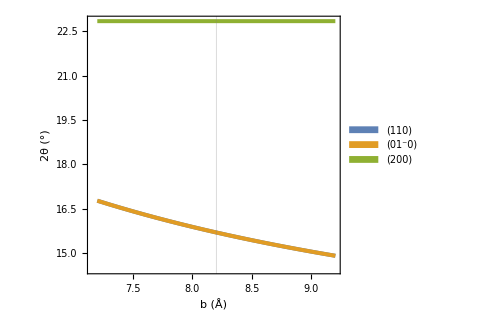

```mathematica
p2=ListLinePlot[{
Table[{ttb2[[i,1]],ttb2[[i,2]]},{i,1,Length[n]}],
Table[{ttb2[[i,1]],ttb2[[i,3]]},{i,1,Length[n]}],
Table[{ttb2[[i,1]],ttb2[[i,4]]},{i,1,Length[n]}]},
GridLines->{{8.201}, None},Frame->True,
FrameLabel->{
Style["b (Å)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.5}],
ImageSize->Medium,AspectRatio->0.9
]
```

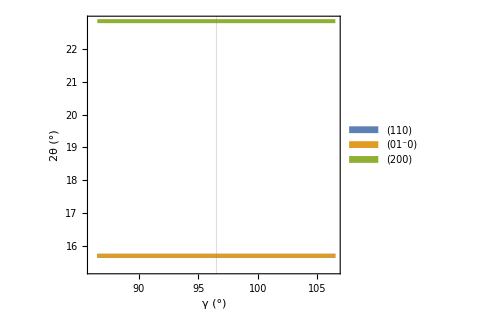

```mathematica
p3=ListLinePlot[{
Table[{ttg2[[i,1]],ttg2[[i,2]]},{i,1,Length[n]}],
Table[{ttg2[[i,1]],ttg2[[i,3]]},{i,1,Length[n]}],
Table[{ttg2[[i,1]],ttg2[[i,4]]},{i,1,Length[n]}]},
GridLines->{{96.5}, None},Frame->True,
FrameLabel->{
Style["γ (°)",FontSize->16,Black,Bold],
Style["2θ (°)",FontSize->16,Black,Bold]
},
(*PlotLabel->Style[None,Bold,FontSize->16,Black],*)
FrameStyle->Black,
FrameTicksStyle->Directive[Black,FontSize->16],
PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008]} ,
PlotLegends->Placed[SwatchLegend[{"(110)",Style[Row[{"(0",Overscript["1","-"],"0)"}],FontSize->16],Style[Row[{"(2",Overscript["0",""],"0)"}],FontSize->16]},LabelStyle->{FontSize->16,Bold,Black}],{0.15,0.5}],
ImageSize->Medium,AspectRatio->0.9
]
```

#### plot

```mathematica
{p1,p2,p3}
```

{-Graphics-,-Graphics-,-Graphics-}

## Storage

```mathematica
ClearAll["Global`*"];
dd[h_,k_,l_,α_,β_,γ_,a_,b_,c_]:=(a b c)/(√(a^2 c^2 k^2-2 a b^2 c h l Cot[° β] Csc[° β]+b^2 c^2 h^2 Csc[° β]^2+a^2 b^2 l^2 Csc[° β]^2));
dd[1,1,0,90,90,γ,a,b,c]
dd[1,-1,0,90,90,γ,a,b,c]
```

(a b c)/(√(a^2 c^2+b^2 c^2))

(a b c)/(√(a^2 c^2+b^2 c^2))

-Graphics-

```mathematica
ClearAll["Global`*"];
Solve[1/d^2==1/Sin[β Degree]^2(h^2/a^2+(k^2*Sin[β Degree]^2)/b^2+l^2/c^2-(2h l Cos[β Degree])/(a c)),d]
```

{{d→-(a b c)/(√(a^2 c^2 k^2-2 a b^2 c h l Cot[° β] Csc[° β]+b^2 c^2 h^2 Csc[° β]^2+a^2 b^2 l^2 Csc[° β]^2))},{d→(a b c)/(√(a^2 c^2 k^2-2 a b^2 c h l Cot[° β] Csc[° β]+b^2 c^2 h^2 Csc[° β]^2+a^2 b^2 l^2 Csc[° β]^2))}}

Nishiyama 2022. J. AM. CHEM. SOC. 2002, 124, 9074-9082

```mathematica
ClearAll["Global`*"]
λ=1.5418;(*Kα1&Kα2*)
{h,k,l}={2,0,0};
{α,β,γ}={90,90,96.5};
{a,b,c}={7.784,8.201,10.380};
(*monoclinic*)
d=(a b c)/(√(a^2 c^2 k^2-2 a b^2 c h l Cot[° β] Csc[° β]+b^2 c^2 h^2 Csc[° β]^2+a^2 b^2 l^2 Csc[° β]^2));
θ=ArcSin[λ/(2d)]*180/π;

Print["d(200)= ",d]
Print["2θ(200) = ",2θ]
```

d(200)= 3.892

2θ(200) = 22.8486

```mathematica
θ2[d_,h_,k_,l_,α_,β_,γ_,a_,b_,c_]:=ArcSin[λ/(2d2[h,k,l,α,β,γ,a,b,c])]*180/π;
```

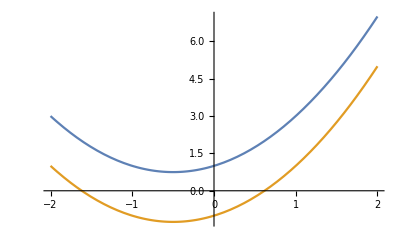

```mathematica
Plot[{{x^2+x+1},{x^2+x-1}},{x,-2,2}]
```

```mathematica
h^2 b^2 c^2+k^2 a^2 c^2 Sin[γ]^2+l^2 a^2 b^2-2h k a b^2 c Cos[γ]^2

(h^2*b^2*c^2*Sin[alpha]^2+k^2*a^2*c^2*Sin[beta]^2+l^2*a^2*b^2*Sin[gamma]^2+2*h*k*a*b^2*c*(Cos[alpha]*Cos[beta]-Cos[gamma])+2*h*l*a*b*c^2*(Cos[beta]*Cos[gamma]-Cos[alpha])+2*k*l*a^2*b*c*(Cos[gamma]*Cos[alpha]-Cos[beta]))/V^2

1/Sqrt[];
```

28986.

(0.+28986. Sin[alpha]^2)/V^2

Sqrt::argx: Sqrt called with 0 arguments; 1 argument is expected.